# Mathematica as a Tool for Astronomy and Physics

## Lecture 10 Wintersemester 2009/10 Markus Röllig

## Calculus

Required Reading

Calculus

### Partial Derivatives

Partial derivatives are produced by the function D[f,x], where the expression f should be either an implicit or explicit function of the variable x for which the derivative is sought.  Partial derivatives with respect to several variables simultaneously are obtained by using a sequence of variables in the argument list.  Multiple derivatives with respect to the same variable are specified by arguments of the form {x,n} where n is the degree of differentiation or by including n instances of x in the sequence of differentiation variables.

There are many equivalent input forms for this function to reflect common usages.  The prime notation is convenient for writing ordinary differential equations and can be entered directly from the keyboard; a slightly more appealing form is obtained by entering Esc'Esc in a superscript box.  The ∂_({x,n},{y,m}) f[x,y] notation is more flexible and more rigorous, superseding the traditional (∂^(n+m) f[x,y])/(∂^n x∂^m y) notation with its cumbersome fractions which do not divide out.  That traditional notation cannot be used without constructing special notation palettes first.  The partial derivative symbol is entered as EscpdEsc  subscripts using Control+_:

The Representation of Derivatives

D[f[x],x]=(∂f[x])/(∂x)=f'[x]=f'[x]=∂_x f[x]
D[f[x],{x,n}]=(∂^n f[x])/(∂x^n)=∂_{x,n} f[x]
D[f[x,y],x,y]=(∂^2 f[x,y])/(∂x∂y)=∂_(x,y) f[x,y]
D[f[x,y],{x,n},{y,m}]=(∂^(n+m) f[x,y])/(∂^n x∂^m y)=∂_({x,n},{y,m}) f[x,y]

```mathematica
D[f[x],x]==f'[x]==f'[x]==D[f[x], x]
```

True

```mathematica
D[f[x],x]
```

f'[x]

```mathematica
D[f[x,y],{x,n},{y,m}]
```

f^(n,m)[x,y]

```mathematica
D[f[x,y], {x,n},{y,m}]
```

f^(n,m)[x,y]

```mathematica
D[f[x], x,x]
```

f''[x]

```mathematica
D[f[x], {x,4}]
```

f^(4)[x]

```mathematica
f''''[x]
```

f^(4)[x]

Notation can also be mixed

```mathematica
D[f[x],x]'
```

f''[x]

D employs all the basic rules for differentiating products and quotients and uses the chain rule.

```mathematica
Clear[f,g]
```

```mathematica
D[f[x] g[x],x]
```

g[x] f'[x]+f[x] g'[x]

```mathematica
D[f[x y],x]
```

y f'[x y]

```mathematica
D[f[g[x]],x]
```

f'[g[x]] g'[x]

```mathematica
D[InverseFunction[f][x],x]
```

1/f'[f^(-1)[x]]

```mathematica
D[∫_a^x f[t]ⅆt,x]
```

f[x]

```mathematica
D[∫_a^Cos[x] f[t]ⅆt,x]
```

-f[Cos[x]] Sin[x]

Here are some more examples of derivatives that Mathematica can do

```mathematica
D[(x^2+1)/(ⅇ^Sin[x] (3 x+5)), x]
```

(2 ⅇ^(-Sin[x]) x)/(5+3 x)-(3 ⅇ^(-Sin[x]) (1+x^2))/(5+3 x)^2-(ⅇ^(-Sin[x]) (1+x^2) Cos[x])/(5+3 x)

Mathematica can also do derivations of  implicit functions

```mathematica
ImplicitEquation=(((y(x))/2^(2/3)-x/2^(2/3)) Ai(((y(x))/2^(2/3)-x/2^(2/3))^2+1/(2^(1/3) x))+Ai'(((y(x))/2^(2/3)-x/2^(2/3))^2+1/(2^(1/3) x)))/(((y(x))/2^(2/3)-x/2^(2/3)) Bi(((y(x))/2^(2/3)-x/2^(2/3))^2+1/(2^(1/3) x))+Bi'(((y(x))/2^(2/3)-x/2^(2/3))^2+1/(2^(1/3) x)))==1;
```

```mathematica
D[ImplicitEquation, x]
```

(AiryAi[1/(2^(1/3) x)+(-x/2^(2/3)+y[x]/2^(2/3))^2] (-1/2^(2/3)+y'[x]/2^(2/3))+AiryAiPrime[1/(2^(1/3) x)+(-x/2^(2/3)+y[x]/2^(2/3))^2] (-x/2^(2/3)+y[x]/2^(2/3)) (-1/(2^(1/3) x^2)+2 (-x/2^(2/3)+y[x]/2^(2/3)) (-1/2^(2/3)+y'[x]/2^(2/3)))+AiryAi[1/(2^(1/3) x)+(-x/2^(2/3)+y[x]/2^(2/3))^2] (1/(2^(1/3) x)+(-x/2^(2/3)+y[x]/2^(2/3))^2) (-1/(2^(1/3) x^2)+2 (-x/2^(2/3)+y[x]/2^(2/3)) (-1/2^(2/3)+y'[x]/2^(2/3))))/(AiryBiPrime[1/(2^(1/3) x)+(-x/2^(2/3)+y[x]/2^(2/3))^2]+AiryBi[1/(2^(1/3) x)+(-x/2^(2/3)+y[x]/2^(2/3))^2] (-x/2^(2/3)+y[x]/2^(2/3)))-((AiryAiPrime[1/(2^(1/3) x)+(-x/2^(2/3)+y[x]/2^(2/3))^2]+AiryAi[1/(2^(1/3) x)+(-x/2^(2/3)+y[x]/2^(2/3))^2] (-x/2^(2/3)+y[x]/2^(2/3))) (AiryBi[1/(2^(1/3) x)+(-x/2^(2/3)+y[x]/2^(2/3))^2] (-1/2^(2/3)+y'[x]/2^(2/3))+AiryBiPrime[1/(2^(1/3) x)+(-x/2^(2/3)+y[x]/2^(2/3))^2] (-x/2^(2/3)+y[x]/2^(2/3)) (-1/(2^(1/3) x^2)+2 (-x/2^(2/3)+y[x]/2^(2/3)) (-1/2^(2/3)+y'[x]/2^(2/3)))+AiryBi[1/(2^(1/3) x)+(-x/2^(2/3)+y[x]/2^(2/3))^2] (1/(2^(1/3) x)+(-x/2^(2/3)+y[x]/2^(2/3))^2) (-1/(2^(1/3) x^2)+2 (-x/2^(2/3)+y[x]/2^(2/3)) (-1/2^(2/3)+y'[x]/2^(2/3)))))/(AiryBiPrime[1/(2^(1/3) x)+(-x/2^(2/3)+y[x]/2^(2/3))^2]+AiryBi[1/(2^(1/3) x)+(-x/2^(2/3)+y[x]/2^(2/3))^2] (-x/2^(2/3)+y[x]/2^(2/3)))^2==0

Surprisingly, this result can be simplified considerably:

```mathematica
Simplify[Solve[%,y'[x]]]
```

{{y'[x]→1+1/(x^2 y[x])}}

#### Excercises

Calculate the first derivate of the function f(x)=2 x^4-x^3+3 x+5x-1 with respect to x
Calculate also the second, third and fourth derivative with respect to x.

Calculate the first derivate of the function f (x) = 2 x^2 y^2-3 x^2 y-2x y+3 y^2 with respect to x.
Calculate ∂_({x,1},{y,2}) f(x), ∂_({x,1},{y,1}) f(x),and ∂_({x,2},{y,1}) f(x)

Locate the extrema of x^3-2 x^2-10x+5.

Find the maximum of x^4/(ⅇ^x+1) for positive x (both position and value).  [Hint: simplify the equation first to eliminate the trivial but spurious solution.  Then use Solve, NSolve, or FindRoot; all should agree!]

Given a function r(t) with values in R^3, the curvature at a given value of t is κ=(|ṙ×r̈|)/(|ṙ|^3) (ṙ=∂_t r(t)). Create a function that takes a 3-dim parametrized curve r(t)= {x(t),y(t),z(t)} and returns the curvature κ(t). (Test it using the helix curve { r Cos[t], r Sin[t], c t}).

### Total derivatives

Required Reading

Total Derivatives

In Mathematica, D[f,x] gives a partial derivative, with all other variables assumed independent of x. Dt[f,x] gives a total derivative, in which all variables are assumed to depend on x. In both cases, you can add an argument to give more information on dependencies.

```mathematica
Dt[f[x,t],t]
```

f^(0,1)[x,t]+Dt[x,t] f^(1,0)[x,t]

```mathematica
Dt[f[x,y,z,t]]
```

Dt[t] f^(0,0,0,1)[x,y,z,t]+Dt[z] f^(0,0,1,0)[x,y,z,t]+Dt[y] f^(0,1,0,0)[x,y,z,t]+Dt[x] f^(1,0,0,0)[x,y,z,t]

This gives the partial derivative ∂/(∂x)(x^2+y^2). y is assumed to be independent of x.

```mathematica
D[x^2+y^2,x]
```

2 x

This gives the total derivative d/dx(x^2+y^2). Now y is assumed to depend on x.

```mathematica
Dt[x^2+y^2,x]
```

2 x+2 y Dt[y,x]

This takes the total derivative, with z held fixed.

```mathematica
Dt[x^2+y^2+z^2,x,Constants->{z}]
```

2 x+2 y Dt[y,x,Constants→{z}]

However, if expressions involve symbols which should always be constant, such as constants of nature, it is best to declare them constants by setting the appropriate attribute.

```mathematica
SetAttributes[{ℏ,m},Constant]
```

```mathematica
Dt[-ℏ^2/(2m)D[ψ[x,t], {x,2}],t]
```

-(ℏ^2 (ψ^(2,1)[x,t]+Dt[x,t] ψ^(3,0)[x,t]))/(2 m)

#### Example: particle in uniform gravity

The energy of a particle in uniform gravity has the form

```mathematica
ClearAll[m,g,x,y,z,t];
energy = m g z[t] + 1/2 m (x'[t]^2+y'[t]^2+z'[t]^2)
```

g m z[t]+1/2 m (x'[t]^2+y'[t]^2+z'[t]^2)

The time dependence of the energy is given by the total derivative

```mathematica
Dt[energy,t]
```

m Dt[g,t] z[t]+g Dt[m,t] z[t]+g m z'[t]+1/2 Dt[m,t] (x'[t]^2+y'[t]^2+z'[t]^2)+1/2 m (2 x'[t] x''[t]+2 y'[t] y''[t]+2 z'[t] z''[t])

However, this result includes derivatives of mass with respect to time which should not appear for a simple particle that neither sheds nor accretes mass.  We specify that m and g are constants using the option Constants, such that

```mathematica
Dt[energy,t,Constants->{m,g}]
```

g m z'[t]+1/2 m (2 x'[t] x''[t]+2 y'[t] y''[t]+2 z'[t] z''[t])

Furthermore, Newton's second law can be used to simplify this result

```mathematica
Dt[energy,t,Constants->{m,g}]/.{x''[t]->0,y''[t]->0,z''[t]->-g}
```

0

The dependence of the energy on height is then seen to vanish; in other words, energy is conserved.

### Locating minima/maxima

Required Reading

Unconstrained Optimization
Numerical Optimization
Minimization and Maximization

The extrema of a function (maxima, minima, and inflection points) can be determined by solving equations, either symbolically or numerically, that set first derivatives to zero and then ascertaining the characteristics of the second derivatives.  Symbolic methods will usually reveal all extrema, while numerical methods search for extrema near a specified starting point.  Mathematica provides a built-in function FindMinimum which searches for a local minimum near the starting point automatically, without the user having to establish the equations for the first derivative or to test the second.  The result is usually the nearest minimum, which may not be the absolute minimum of the function — it is simply a nearby local minimum.  If you need an absolute minimum, it is usually necessary to examine the function graphically in order to supply a reasonably good starting value or set of starting values.  You also need to check that the result truly is the desired minimum — sometimes FindMinimum wanders away from your starting values and sometimes it returns incorrect results.

The basic syntax is FindMinimum[f,{x,x_0}] where f  is a function of x and x_0 is the starting value.  The function must evaluate to a real number given a numerical value for x.  You can limit the range of x by including xmin, xmax after x_0.

```mathematica
Clear[f];
f=(1+x-x^2) Exp[-x^2/4];
```

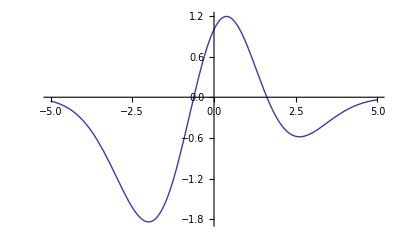

```mathematica
Plot[f,{x,-5,5}]
```

The positive minimum is found using an appropriate choice of x.  The result is returned as a list whose first element is the value of the function as the minimum and the second is a list of replacement rules specifying the location of the minimum.

```mathematica
FindMinimum[f,{x,3}]
```

{-0.583234,{x→2.61803}}

Like FindRoot, FindMinimum and FindMaximum work by starting from a point, then progressively searching for a minimum or maximum. But since they return a result as soon as they find anything, they may give only a local minimum or maximum of your function, not a global one.

This curve has two local minima.

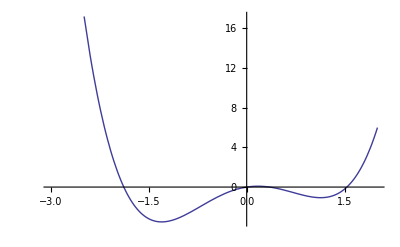

```mathematica
Plot[x^4-3x^2+x,{x,-3,2}]
```

Starting at x=1, you get the local minimum on the right.

```mathematica
FindMinimum[x^4-3 x^2+x,{x,1}]
```

{-1.07023,{x→1.1309}}

This gives the local minimum on the left, which in this case is also the global minimum.

```mathematica
FindMinimum[x^4-3 x^2+x,{x,-1}]
```

{-3.51391,{x→-1.30084}}

If you want to search for global Minima/Maxima Mathematica offers different functions.

This immediately finds the global minimum.

```mathematica
NMinimize[x^4-3x^2+x,x]
```

{-3.51391,{x→-1.30084}}

NMinimize and NMaximize are numerical analogs of Minimize and Maximize. But unlike Minimize and Maximize they usually cannot guarantee to find absolute global minima and maxima. Nevertheless, they typically work well when the function f is fairly smooth, and has a limited number of local minima and maxima.

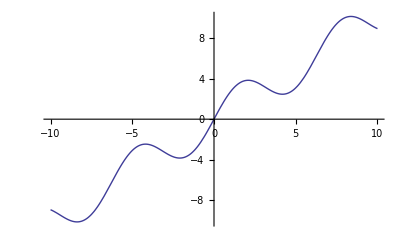

```mathematica
Plot[x+2 Sin[x],{x,-10,10}]
```

```mathematica
Maximize[{x+2 Sin[x],-10<=x<=10},x]//N
```

{10.1096,{x→8.37758}}

Minimize and Maximize yield lists giving the value attained at the minimum or maximum, together with rules specifying where the minimum or maximum occurs.

```mathematica
Minimize[x^2-3x+6,x]
```

{15/4,{x→3/2}}

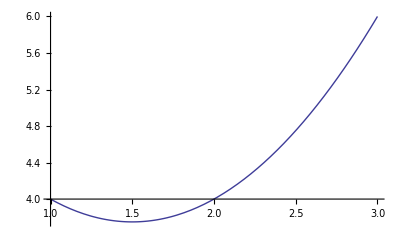

```mathematica
Plot[x^2-3x+6,{x,1,3}]
```

This maximizes with respect to x and y.

```mathematica
Maximize[5 x y-x^4-y^4,{x,y}]
```

{25/8,{x→-(√5)/2,y→-(√5)/2}}

Minimize[expr,x] minimizes expr allowing x to range over all possible values from -∞ to +∞. Minimize[{expr,cons},x] minimizes expr subject to the constraints cons being satisfied. The constraints can consist of any combination of equations and inequalities.

This finds the maximum within the unit circle.

```mathematica
Maximize[{5 x y-x^4-y^4,x^2+y^2<=1},{x,y}]
```

{2,{x→-1/(√2),y→-1/(√2)}}

This finds the maximum along a line.

```mathematica
Maximize[{5 x y-x^4-y^4,x+y==1},{x,y}]
```

{9/8,{x→1/2,y→1/2}}

This does maximization only over integer values of x and y.

```mathematica
Maximize[{x y,x^2+y^2<120&&(x|y) ∈ Integers},{x,y}]
```

{56,{x→-7,y→-8}}

#### Example: Minimal sum of squares

Take 1000 points scattered around a circle.

```mathematica
SeedRandom[999];
```

```mathematica
With[{δ = 0.1},
circleData = Table[
  Function[φ, {Cos[φ], Sin[φ]} + 
            {Random[Real, {-δ, δ}], Random[Real, {-δ, δ}]}][
                           Random[Real, {0, 2Pi}]], {1000}]];
```

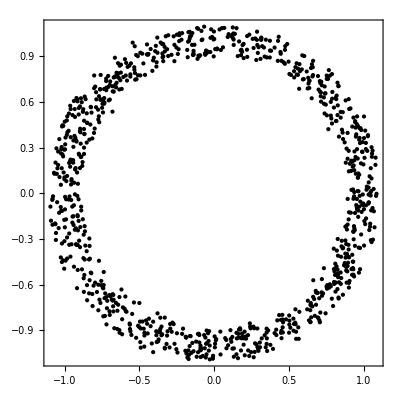

```mathematica
Show[Graphics[Point /@ circleData],
     PlotRange -> All, Frame -> True, AspectRatio -> Automatic]
```

We want to find the circle, such that the sum of the squares of the distances of the points to this circle becomes minimal. The function distance measures the distance between a circle and a point

```mathematica
distance[Circle[{mpx_, mpy_}, r_], point:{x_, y_}] :=
With[{R = Sqrt[(mpx - x)^2 + (mpy - y)^2]}, Sqrt[(r - R)^2]]
```

These data yield the following function to be minimized.

```mathematica
toMinimize = Plus @@ (distance[Circle[{mpx, mpy}, r], #]^2& /@ circleData);
```

```mathematica
{#, Timing[FindMinimum[toMinimize, {mpx, 1}, {mpy, 1}, {r, 2},
                   Method -> #]]}& /@ 
       Append[{"Gradient", "Newton", "QuasiNewton", "ConjugateGradient"},
              "LevenbergMarquardt"]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{Gradient,{0.577,{3.57338,{mpx→-0.000104213,mpy→0.000960085,r→1.00334}}}},{Newton,{1.107,{3.57338,{mpx→-0.000104475,mpy→0.000960514,r→1.00334}}}},{QuasiNewton,{0.453,{3.57338,{mpx→-0.000104475,mpy→0.000960515,r→1.00334}}}},{ConjugateGradient,{0.546,{3.57338,{mpx→-0.000104475,mpy→0.000960515,r→1.00334}}}},{LevenbergMarquardt,{0.452,{3.57338,{mpx→-0.000104477,mpy→0.000960511,r→1.00334}}}}}

Here is the calculated circle together with the original points.

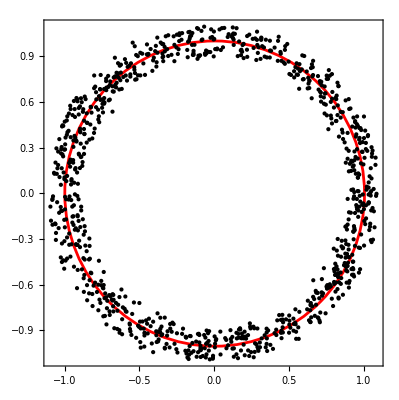

```mathematica
Show[Graphics[{{Hue[0], Thickness[0.005], 
                Circle[{mpx, mpy}, r] /. %[[-1, -1, -1, -1]]},
               {GrayLevel[0], Point /@ circleData}}],
     PlotRange -> All, Frame -> True, AspectRatio -> Automatic]
```

#### Excercises

Find the global maximum of -1.5 x^4 - 3 x^2 + x

If n equally spaced identical antennas radiate in phase, the angular distribution is described by an interference pattern of the form
f[n,α]=Sin[n α]^2/Sin[α]^2
where
α = d/λ Sin[θ]
and where d is the spacing between sources and λ is the wave length.
a) Plot the distribution in α for several values of n and determine the locations of the principal maxima.  How many minor maxima are found between principal maxima?
b) Write a function which produces a numerical list of positions for the minor maxima. with 0<α<π.

The angle, θ, between two curves, y_1[x] and y_2[x], at a point of intersection is defined as the angle between the tangents at that point.
a) Derive a formula for Tan[θ] in terms of the slopes m_i=ⅆ y_i/ⅆx.
b) Recall the "cylinder in a trough" problem from the algebra notebook.  A cylinder of radius R is dropped into a parabolic trough and becomes wedged when its center is at height h.  Another way to determine h is to evaluate the angle between the curves x^2+(y-h)^2=R^2 and y=a x^2 at their points of intersection.  Clearly, this angle should be zero at the proper value of h.

### Taylor Series, Limits

Required Reading

Series Expansions

Series[f,{x,0,n}] constructs Taylor series for any function f according to the formula f(0)+f'(0)x+f''(0)x^2/2+…f^(n)(0)x^n/n!. Series can construct standard Taylor series, as well as certain expansions involving negative powers, fractional powers and logarithms. Normal[series] truncates a power series and converts it to a normal expression.

```mathematica
Series[Exp[x],{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
Normal[%]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800

Power series of an arbitrary function around x=a:

```mathematica
Series[f[x],{x,a,3}]
```

(ⅇ^(-x^2/4) (1+x-x^2))[x]

```mathematica
Series[Exp[-a t] (1+Sin[2 t]),{t,0,4}]
```

1+(2-a) t+(-2 a+a^2/2) t^2+(-4/3+a^2-a^3/6) t^3+1/24 (32 a-8 a^3+a^4) t^4+O[t]^5

```mathematica
Series[BesselJ[n,x],{x,0,4}]
```

x^n (2^-n/Gamma[1+n]-(2^(-2-n) x^2)/((1+n) Gamma[1+n])+(2^(-5-n) x^4)/((1+n) (2+n) Gamma[1+n])+O[x]^5)

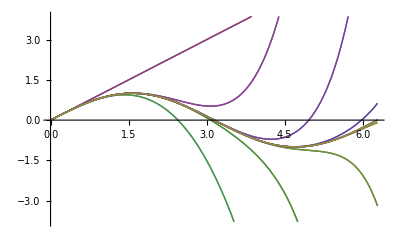

```mathematica
Plot[Evaluate[Table[Normal[Series[Sin[x],{x,0,n}]],{n,20}]],{x,0,2Pi}]
```

Piecewise functions:

```mathematica
Series[Min[x,1-x],{x,a,5}]
```

Piecewise[{{(1-a)-(x-a)+O[x-a]^6, x∈Reals&&a>1/2}, {a+(x-a)+O[x-a]^6, x∈Reals&&a<1/2}, {(1-a)-(x-a)+O[x-a]^6, a==1/2&&x≥1/2}, {a+(x-a)+O[x-a]^6, True}}]

If you give it a function that it does not know, Series writes out the power series in terms of derivatives.

```mathematica
Series[1+f[t],{t,0,3}]
```

(1+(ⅇ^(-x^2/4) (1+x-x^2))[0])+(ⅇ^(-x^2/4) (1+x-x^2))'[0] t+1/2 (ⅇ^(-x^2/4) (1+x-x^2))''[0] t^2+1/6 (ⅇ^(-x^2/4) (1+x-x^2))^(3)[0] t^3+O[t]^4

Series[f,{x,x_0,n_x},{y,y_0,n_y},…] successively finds series expansions with respect to x, then y, etc.

```mathematica
Series[Sin[x+y],{x,0,3},{y,0,3}]
```

(y-y^3/6+O[y]^4)+(1-y^2/2+O[y]^4) x+(-y/2+y^3/12+O[y]^4) x^2+(-1/6+y^2/12+O[y]^4) x^3+O[x]^4

Limit[expr,x->x_0] tells you what the value of expr is when x tends to x_0. When this value is infinite, it is often useful instead to know the residue of expr when x equals x_0. The residue is given by the coefficient of (x-x_0)^-1 in the power series expansion of expr about the point x_0.

```mathematica
Limit[1/x,x->0]
```

∞

```mathematica
Residue[1/x,{x,0}]
```

1

```mathematica
Limit[(2 n^2+5)/(3 n^2+1),n->∞]
```

2/3

Directional limits can be obtained for some functions.

```mathematica
Limit[1/x,x->0,Direction->-1]
```

∞

```mathematica
Limit[1/x,x->0,Direction->+1]
```

-∞

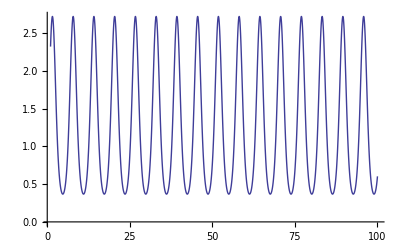

```mathematica
Plot[Exp[Sin[x]],{x,1,100}]
```

```mathematica
Limit[Exp[Sin[x]], x->∞]
```

Interval[{1/ⅇ,ⅇ}]

#### Excercise

Let U[y]=Tanh[y] or U[τ]=Tanh[1/τ] be two representations of the same function.  Compare the Taylor expansion of U[y] for small y with the Taylor expansion of U[τ] for large τ (expand about ∞).

Use series expansions to characterize the behavior of f[z]=1-z/(√(z^2+R^2)) for both small and large values of z, assuming that R>0.  Compare these approximations with the original function graphically and describe their regions of validity.  How does one obtain a useful approximation for z≈R?

Find the residue of x tan(x) at π/2.

Evaluate the limit of Tanh[1/x] as x→0.  How does the result depend upon direction?

Compare the behaviors of BesselJ[2,z] and BesselK[2,z] as z→∞.

### Symbolic Integration

Required Reading 

Integration
Indefinite Integrals

Here is the integral ∫x^n dx in Mathematica.

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

This integral involves Erf.

```mathematica
Integrate[Exp[1-x^2],x]
```

1/2 ⅇ √π Erf[x]

And this one involves a Fresnel function.

```mathematica
Integrate[Sin[x^2],x]
```

√(π/2) FresnelS[√(2/π) x]

Here is the definite integral ∫_a^b sin^2(x) dx.

```mathematica
Integrate[Sin[x]^2,{x,a,b}]
```

1/2 (-a+b+Cos[a] Sin[a]-Cos[b] Sin[b])

Mathematica cannot give you a formula for this definite integral.

```mathematica
Integrate[x^x,{x,0,1}]
```

∫_0^1 x^x ⅆx

You can still get a numerical result, though.

```mathematica
N[%]
```

0.783431

This evaluates the multiple integral ∫_0^1 dx∫_0^x dy (x^2+y^2). The range of the outermost integration variable appears first.

```mathematica
Integrate[x^2 + y^2, {x, 0, 1}, {y, 0, x}]
```

1/3

Multiple integral with x integration outermost:

```mathematica
Integrate[Sin[x y],{x,0,1},{y,0,x}]
```

1/2 (EulerGamma-CosIntegral[1])

```mathematica
∫_0^1 ∫_0^x Sin[x y]ⅆyⅆx
```

1/2 (EulerGamma-CosIntegral[1])

Use Esc int Esc to enter ∫ and Esc dd Esc to enter ⅆ:

```mathematica
∫Sqrt[x+Sqrt[x]]ⅆx
```

1/12 √(√x+x) (-3+2 √x+8 x)+1/8 Log[1+2 √x+2 √(√x+x)]

Use Ctrl+_ to enter the lower limit, then Ctrl+% for the upper limit:

```mathematica
∫_0^∞ Log[x] Exp[-x^2]ⅆx
```

-1/4 √π (EulerGamma+Log[4])

Some more examples (The Airy function Ai(z) is a solution to the differential equation y''-xy=0. ):

```mathematica
∫Ai(z)ⅆz
```

-(z (-3 Gamma[1/3] Gamma[5/3] HypergeometricPFQ[{1/3},{2/3,4/3},z^3/9]+3^(1/3) z Gamma[2/3]^2 HypergeometricPFQ[{2/3},{4/3,5/3},z^3/9]))/(9 3^(2/3) Gamma[2/3] Gamma[4/3] Gamma[5/3])

```mathematica
∫_0^∞ (sin(x^3))/ⅇ^(x/2)ⅆx
```

1/72 (3 HypergeometricPFQ[{1},{2/3,5/6,7/6,4/3},-1/746496]-4 π ((1+√3) KelvinBei[-1/3,1/(3 √6)]+(-1+√3) KelvinBei[1/3,1/(3 √6)]-KelvinBer[-1/3,1/(3 √6)]+√3 KelvinBer[-1/3,1/(3 √6)]+KelvinBer[1/3,1/(3 √6)]+√3 KelvinBer[1/3,1/(3 √6)]))

```mathematica
∫_0^∞ (sin(x) sin(x/3) sin(x/5) sin(x/7) sin(x/9) sin(x/11) sin(x/13) sin(x/15) sin(x/17))/x^9 ⅆx
```

(17708695183056190642497315530628422295569865119 π)/1220462921565155916674902677397230198502690752000000000

#### Excercises

Calculate ∫dx/(x^2-1). Then differentiate the result and check that you get the original function back. Consider simplifying your result.

Calculate the integral ∫sin(x^3)ⅆx.

Calculate the integrals ∫_0^1 sin(x^3)ⅆx, ∫_0^∞ sin(x^3)ⅆx, and ∫_(-∞)^1 sin(x^3)ⅆx.

Determine the area of the region bounded between the curves f (x) =sin x and g(x) =csc^2 x on [π/ 4, 3 π/ 4].

Determine the area of the region enclosed between the curves f (x) =x(x^2 -3 x +3) and g(x) =x^2.

### Advanced Application: Line integrals

A line integral evaluates and integrates a function along a specified path through a multidimensional space, returning a scalar result.  Here we consider two types of line integral.  The integral of scalar function against the path length for a curve in two dimensions takes the form

∫_C f[x,y]ⅆs

where C denotes a curve and ⅆs=√((ⅆx)^2+(ⅆy)^2) represents the path length along the curve.  The curve is generally represented by the parametric equations C={x→x[t],y→y[t]} such that the path length becomes ⅆs=ⅆt √((ⅆx/ⅆt)^2+(ⅆy/ⅆt)^2).  For example, if f represents mass density, an integral of this type could be used to determine the total mass of a rope with nonuniform density or cross-sectional area.

Similarly, the component of a vector field that is parallel to a curve is integrated using

∫_C f⃗[x,y].ⅆ s⃗

where ⅆ s⃗=ⅆt{ⅆx/ⅆt,ⅆy/ⅆt} is the differential displacement along the curve.  For example, the work performed by a force f⃗ that acts on a particle whose trajectory is described by the parametric curve C={x→x[t],y→y[t]} is given by an integral of this type.
The following function evaluates these types of path integrals symbolically.  Here we present a relatively simple implementation and do not attempt to cover all possible methods for specifying the function or path.  The path-integration function can be generalized later if needed.  We assume that the function is an implicit function of the two variables represented by patterns x_ and y_.  The path is defined using a pattern argument path:{pattern rules} in which the pattern rules are a list of rewrite rules of the form x_→u_ that replace the variable on the lhs by the pattern on the rhs; hence, blank patterns are used on both sides of the arrow.  The parameter defining the progress along the curve is given by t_.  Two versions are given, one for scalar functions and the other for vector functions in two dimensions.  Obviously, it is simple matter to generalize to arbitrary dimensionality.

```mathematica
ClearAll[pathIntegrate]
```

```mathematica
pathIntegrate::usage="pathIntegrate[f,{x→u,y→v},t,tmin,tmax,opts] evaluates the line integral of the scalar function f along a curve expressed as a parametric function of t. \n\n pathIntegrate[{fx,fy},{x→u,y→v},t,tmin,tmax] evaluates the line integral of the tangential component of a vector field along a curve expressed as a parametric function of t.";
		
		
pathIntegrate[f_/;(Not[VectorQ[f]]),path:{x_->u_,y_->v_},t_,tmin_,tmax_,opts___Rule] :=Integrate[f √(D[u,t]^2+D[v,t]^2)/.path,{t,tmin,tmax},opts];

pathIntegrate[field:{f_,g_},path:{x_->u_,y_->v_},t_,tmin_,tmax_,opts___Rule] :=Integrate[(f D[u,t]+g D[v,t])/.path,{t,tmin,tmax},opts]
```

#### Application

```mathematica
pathIntegrate[1/(x^2+y^2),{x->Cos[t],y->Sin[t]},t,0,2π]
```

2 π

```mathematica
pathIntegrate[1/(x^2+y^2),{x->t,y->t},t,1,2]
```

1/(2 √2)

```mathematica
pathIntegrate[1/(x^2+y^2),{x->a +t,y->b t},t,0,1,Assumptions->{a∈Reals,b∈Reals}]
```

√(1+b^2) If[((a Re[1/(ⅈ+b)]≠0||a Im[1/(ⅈ+b)]≥1)&&(a Im[1/(-ⅈ+b)]==0||a Re[1/(-ⅈ+b)]≠0||1+a Im[1/(-ⅈ+b)]≤0))||a≥0,(-ArcCot[b]+ArcCot[(a b)/(1+a+b^2)])/(a b),Integrate[1/(b^2 t^2+(a+t)^2),{t,0,1},Assumptions→b==0&&-1<a<0]]

```mathematica
pathIntegrate[{x^2,y},{x->t,y->t},t,0,2]
```

14/3

```mathematica
pathIntegrate[{x^2,y},{x->2Sin[t],y->2Sin[t]},t,0,π/2]
```

14/3

```mathematica
pathIntegrate[{y,x},{x->a t^n,y->b t^m},t,0,1]
```

If[Re[m+n]>0,a b,Integrate[a b m t^(-1+m+n)+a b n t^(-1+m+n),{t,0,1},Assumptions→Re[m+n]≤0]]

#### Excercises

Write line integration functions applicable to arbitrary dimensionality.

Proper time
Proper time ∫_C ⅆτ in special relativity is defined by a path length through space-time based upon the invariant interval (ⅆτ)^2= (ⅆt)^2-(ⅆx)^2-(ⅆy)^2-(ⅆz)^2.  Write a function which computes the proper time for an arbitrary path in space-time.  One can show that the proper time measures the aging of a particle (or person) in its own rest frame.  However, the elapsed times for other observers who see the particle moving can be quite different.  Compare the proper times for the following two paths, which are relevant to the famous twin paradox.  Peter remains on earth while Paul travels at 99% of light speed away from earth for 25 earth years and then turns instantly and returns at the same speed.  Show that qualitatively similar results are obtained for more realistic itineraries (without incredible acceleration near the turn).

### Numerical Integration

Required Reading 

Numerical Operations on Functions
Numerical Integration
Advanced Numerical Integration in Mathematica
NIntegrate Integration Strategies
The Uncertainties of Numerical Mathematics

Compute a numerical integral:

```mathematica
NIntegrate[Sin[Sin[x]],{x,0,2}]
```

1.24706

Compute a multidimensional integral (with singularity at the origin):

```mathematica
NIntegrate[1/(√(x1/3+x2/2+x3/2+x4/10)),{x1,0,1},{x2,0,1},{x3,0,1},{x4,0,1}]
```

1.2391

Sometimes, Mathematica will not be able to find results for symbolic interals, or it will take a very long time. 
NIntegrate[f,{x,x_min,x_max}] gives a numerical approximation to the integral ∫_x_min^x_max f dx.

Check the computation Time for the following integral:

```mathematica
Integrate[1/(√Sin[x^2+y]),{x,-2,4},{y,-2,4}]//AbsoluteTiming
```

{102.812145,∫_-2^4 2 (EllipticF[1/4 (4+π-2 x^2),2]+EllipticF[2-π/4+x^2/2,2])ⅆx}

Since this is a definite integral we can also ask for the numerical result:

```mathematica
%//N
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.844958691966859`15.954589770191005}. NIntegrate obtained 30.49309074709632`  - 29.90722149530213` ⅈ and 0.00217692 for the integral and error estimates.

{102.812,30.4931-29.9072 ⅈ}

However, it is much more efficient to use the numerical integration capabilities of Mathematica:

```mathematica
NIntegrate[1/(√Sin[x^2+y]),{x,-2,4},{y,-2,4},Exclusions->(Sin[x^2+y]==0)]//AbsoluteTiming
```

{2.770004,30.4933-29.9073 ⅈ}

Here we excluded the cases where the denominator is 0.

We already saw the following integral:

```mathematica
∫_0^∞ (sin(x) sin(x/3) sin(x/5) sin(x/7) sin(x/9) sin(x/11) sin(x/13) sin(x/15) sin(x/17))/x^9 ⅆx
```

(17708695183056190642497315530628422295569865119 π)/1220462921565155916674902677397230198502690752000000000

```mathematica
N[%]
```

4.55839×10^-8

```mathematica
Quiet[NIntegrate[(Sin[x] Sin[x/3] Sin[x/5] Sin[x/7] Sin[x/9] Sin[x/11] Sin[x/13] Sin[x/15] Sin[x/17])/x^9,{x,0,∞}]]
```

4.55839×10^-8

#### Numerical contour integration

Contour integration along a path defined as a series of connected line segments can be performed using the syntax NIntegrate[f,{z,z_1,z_2,⋯,z_n}] where the z_i are complex numbers that plot the contour.  For example, the following integral is performed along a square contour centered on the origin with edges parallel to the real and imaginary axis.

```mathematica
NIntegrate[Exp[z]/z,{z,-1-ⅈ,1-ⅈ,1+ⅈ,-1+ⅈ,-1-ⅈ}]
```

-6.93889×10^-18+6.28319 ⅈ

Because we chose a function exhibiting only one simple pole with unit residue inside the contour, the result is just 2π ⅈ.  Complex analysis tells us that the same result should be obtained for any other contour which encompasses the same poles and which can be deformed continuously into the first without crossing singularities or branch cuts.  Thus, the diamond-shaped contour

```mathematica
NIntegrate[Exp[z]/z,{z,-1,-ⅈ,1,ⅈ,-1}]
```

0.+6.28319 ⅈ

does indeed give the same result.

#### Excercise

Consult the help pages for Integrate and NIntegrate to understand the difference between N[Integrate[expr,{x,x_min,x_max}]] and NIntegrate[expr,{x,x_min,x_max}]

Green's Theorem: The area enclosed by a parametric curve u(t)={x(t),y(t)} with endpoints u(t0)=u(t1) is given by the line integrals ∮_t0^t1 x ẏ ⅆt. 
a) Give the parametric form of the unit circle and calculate the area using NIntegrate and the Green's Theorem. Plot the circle using ParametricPlot
b) Plot the parametric equations below and calculate the enclosed area.
x(t) = Cos[t] + 1/7 Cos[7 t + Pi/3]; 
y(t) = Sin[t] + 1/7 Sin[7 t];

Compare symbolic and numerical evaluations of ∫_0^1 (ω^4 ⅇ^ω)/((ⅇ^ω-1)^2).

Evaluate ∫_0^∞ (ω^4 ⅇ^ω)/((ⅇ^ω-1)^2) numerically.  [Hint: use LogPlot to examine the integrand.]

### Sums, Products

Required Reading:

Sums and Products
Summation of Series
Introduction to Numerical Sums, Products and Integrals

Sum[f,{i,i_min,i_max}]	the sum ∑_(i=i_min)^i_max f
Sum[f,{i,i_min,i_max,di}]	the sum with i increasing in steps of di
Sum[f,{i,i_min,i_max},{j,j_min,j_max}]	the nested sum ∑_(i=i_min)^i_max ∑_(j=j_min)^j_max f
Product[f,{i,i_min,i_max}]	the product ∏_(i=i_min)^i_max f

```mathematica
Sum[x^i/i,{i,7}]
```

x+x^2/2+x^3/3+x^4/4+x^5/5+x^6/6+x^7/7

```mathematica
Sum[i^2,{i,1,n}]
```

1/6 n (1+n) (1+2 n)

Sum[f,i]gives the indefinite sum ∑_i f.

```mathematica
Sum[i^3,i]
```

1/4 (-1+i)^2 i^2

The following series defines the exponential function.

```mathematica
∑_(n=0)^∞ x^n/(n!)
```

ⅇ^x

The harmonic series is divergent.

```mathematica
∑_(n=1)^∞ 1/n
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ 1/n

```mathematica
∑_(n=0)^∞ (ⅇ^-n ({{2 n}, {n}}) (2/11)^n)/(n+3)
```

1/480 (1331 ⅇ^3-44 ⅇ^(3/2) √(11 (-8+11 ⅇ))-121 ⅇ^(5/2) √(11 (-8+11 ⅇ))-24 √(11 ⅇ (-8+11 ⅇ)))

Approximate an infinite product numerically and symbolically:

```mathematica
NProduct[(1+1/i^2),{i,1,∞}]
```

3.67608

```mathematica
Product[(1+1/i^2),{i,1,∞}]
```

Sinh[π]/π

The following product is evaluated in terms of special functions.

```mathematica
∏_(k=1)^n (3 k-1)^(3 k-1) ⅇ^-k
```

(3^(1/24 (1+6 n)^2) ⅇ^(1/36 (3-18 n (1+n)-2 √3 π+(3 √3 PolyGamma[1,1/3])/π+108 Zeta^(1,0)[-1,2/3+n])))/Glaisher

#### Excercise

Sum the infinite series x^n/n!

Find expressions for the sums of powers of natural numbers a)n	b) n^2	c) n^3

Calculate m ∑_(i=0)^∞ 1/(i^2+5) symbolically (Sum) and numerically (NSum)

Calculate  ∏_(i=1)^∞ (4 i^2)/(4 i^2-1) symbolically (Product) and numerically (NProduct)

### Integral Transforms

Required Reading:

Integral Transforms
Integral Transforms and Related Operations
Discrete Fourier Transforms
Fourier Analysis
Discrete Fourier Transforms

The Laplace transform of a function f(t) is given by ∫_0^∞ f(t)e^-st ⅆt. The inverse Laplace transform of F(s) is given for suitable γ by 1/(2πi)∫_(γ-i∞)^(γ+i∞) F(s)e^st ⅆs.

LaplaceTransform[expr,t,s] gives the Laplace transform of expr.  InverseLaplaceTransform[expr,s,t] gives the inverse Laplace transform of expr.

```mathematica
LaplaceTransform[a x^2+b x +c,x,s]
```

(2 a)/s^3+b/s^2+c/s

```mathematica
LaplaceTransform[t^4 Sin[t],t,s]
```

(24 (1-10 s^2+5 s^4))/((1+s^2)^5)

```mathematica
InverseLaplaceTransform[%,s,t]
```

t^4 Sin[t]

```mathematica
LaplaceTransform[BesselJ[3,t],t,s]
```

1/(√(1+s^2) (s+√(1+s^2))^3)

Laplace transforms have the property that they turn integration and differentiation into essentially algebraic operations. They are therefore commonly used in studying systems governed by differential equations.

```mathematica
LaplaceTransform[Integrate[f[u],{u,0,t}],t,s]
```

LaplaceTransform[(ⅇ^(-x^2/4) (1+x-x^2))[t],t,s]/s

For many purposes (e.g., analyzing data), Fourier analysis is an extremely valuable tool. Given a periodic function f(x) given on 0≤x<L (with period L), whose values f_k=f(x_k) are given at the n points x_k=(k-1)L/n, k=1,2,…,n (and nowhere else), we seek to interpolate these function values using trigonometric functions, that is, as a linear combination of the functions ϕ_l(x)=n^(-1/2)e^(-2πi(l-1)x/L), j=1,…,m. Thus, the expansion has the form f(x)=∑_(j=1)^n c_j ϕ_j(x).

Because ∑_(j=1)^n ϕ_l(x_j)ϕ_k(x_j)=δ_("lk"), we get easily c_k=n^(-1/2)∑_(j=1)^n f_j exp(2π i(j-1)(k-1)/n).

In Mathematica the Fourier transform of a function f(t) is by default defined to be 1/(√(2π))∫_(-∞)^∞ f(t) e^iωt ⅆt. The inverse Fourier transform of F(ω) is similarly defined as 1/(√(2π))∫_(-∞)^∞ F(ω) e^-iωt ⅆω.

FourierTransform[expr,t,ω] gives the symbolic Fourier transform of expr.

```mathematica
FourierTransform[1,t,ω]
```

√(2 π) DiracDelta[ω]

```mathematica
FourierTransform[1/(1+t^2),t,ω]
```

ⅇ^(-Abs[ω]) √(π/2)

```mathematica
FourierTransform[Sin[t],t,ω]
```

ⅈ √(π/2) DiracDelta[-1+ω]-ⅈ √(π/2) DiracDelta[1+ω]

In different scientific and technical fields different conventions are often used for defining Fourier transforms. The option FourierParameters in Mathematica allows you to choose any of these conventions you want.

```mathematica
FourierTransform[1,t,ω]
```

√(2 π) DiracDelta[ω]

Convention for pure mathematics, systems engineering:

```mathematica
FourierTransform[1,t,ω,FourierParameters->{1,-1}]
```

2 π DiracDelta[ω]

Convention for classical physics:

```mathematica
FourierTransform[1,t,ω,FourierParameters->{-1,1}]
```

DiracDelta[ω]

This evaluates a two-dimensional Fourier transform.

```mathematica
FourierTransform[(u v)^2 Exp[-u^2-v^2],{u,v},{a,b}]
```

1/32 (-2+a^2) (-2+b^2) ⅇ^(-a^2/4-b^2/4)

Application: The power spectrum of a damped sinusoid:

(50000 √(2/π))/(100000001-20 ⅈ ω-100 ω^2)

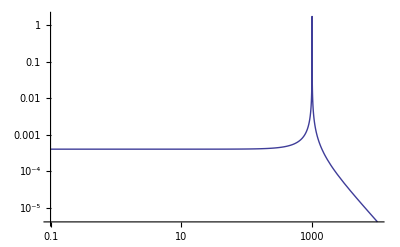
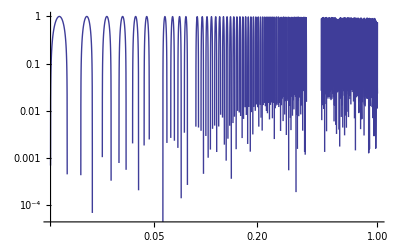

```mathematica
FourierTransform[Sin[10^3 t]Exp[-t/10]UnitStep[t],t,ω]
{LogLogPlot[Evaluate@Abs[%],{ω,1*^-1,1*^4},PlotRange->All],LogLogPlot[Sin[10^3 t]Exp[-t/10]UnitStep[t],{t,0.01,1},PlotRange->All]}
```

FourierSeries[expr,t,n]gives the n^th–order Fourier series expansion of expr in t. 
FourierCoefficient[expr,t,n]  gives the n^th coefficient in the Fourier series expansion of expr.

1/2 ⅈ ⅇ^(-ⅈ t)-1/2 ⅈ ⅇ^(ⅈ t)-1/4 ⅈ ⅇ^(-2 ⅈ t)+1/4 ⅈ ⅇ^(2 ⅈ t)+1/6 ⅈ ⅇ^(-3 ⅈ t)-1/6 ⅈ ⅇ^(3 ⅈ t)

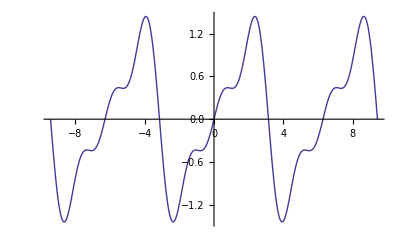

```mathematica
FourierSeries[t/2,t,3]
Plot[%,{t,-3Pi,3Pi}]
```

```mathematica
FourierSeries[t^2+t,t,3]
```

(-2+ⅈ) ⅇ^(-ⅈ t)-(2+ⅈ) ⅇ^(ⅈ t)+(1/2-ⅈ/2) ⅇ^(-2 ⅈ t)+(1/2+ⅈ/2) ⅇ^(2 ⅈ t)-(2/9-ⅈ/3) ⅇ^(-3 ⅈ t)-(2/9+ⅈ/3) ⅇ^(3 ⅈ t)+π^2/3

```mathematica
FourierCoefficient[t^2+t,t,3]
```

-2/9-ⅈ/3

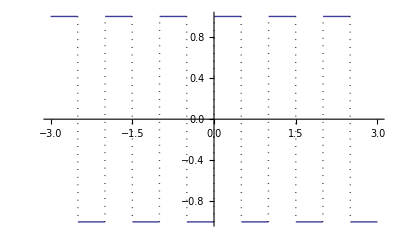

```mathematica
Plot[SquareWave[x],{x,-3,3},ExclusionsStyle->Dotted]
```

```mathematica
FourierSinSeries[SquareWave[x],x,10,FourierParameters->{1,2Pi}]
```

(4 Sin[2 π x])/π+(4 Sin[6 π x])/(3 π)+(4 Sin[10 π x])/(5 π)+(4 Sin[14 π x])/(7 π)+(4 Sin[18 π x])/(9 π)

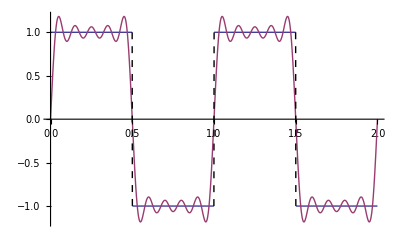

```mathematica
Plot[{SquareWave[x],%},{x,0,2},ExclusionsStyle->Dashed]
```

1/2-(ⅈ ⅇ^(-2 ⅈ π x))/(2 π)+(ⅈ ⅇ^(2 ⅈ π x))/(2 π)-(ⅈ ⅇ^(-4 ⅈ π x))/(4 π)+(ⅈ ⅇ^(4 ⅈ π x))/(4 π)-(ⅈ ⅇ^(-6 ⅈ π x))/(6 π)+(ⅈ ⅇ^(6 ⅈ π x))/(6 π)-(ⅈ ⅇ^(-8 ⅈ π x))/(8 π)+(ⅈ ⅇ^(8 ⅈ π x))/(8 π)-(ⅈ ⅇ^(-10 ⅈ π x))/(10 π)+(ⅈ ⅇ^(10 ⅈ π x))/(10 π)-(ⅈ ⅇ^(-12 ⅈ π x))/(12 π)+(ⅈ ⅇ^(12 ⅈ π x))/(12 π)-(ⅈ ⅇ^(-14 ⅈ π x))/(14 π)+(ⅈ ⅇ^(14 ⅈ π x))/(14 π)-(ⅈ ⅇ^(-16 ⅈ π x))/(16 π)+(ⅈ ⅇ^(16 ⅈ π x))/(16 π)-(ⅈ ⅇ^(-18 ⅈ π x))/(18 π)+(ⅈ ⅇ^(18 ⅈ π x))/(18 π)-(ⅈ ⅇ^(-20 ⅈ π x))/(20 π)+(ⅈ ⅇ^(20 ⅈ π x))/(20 π)

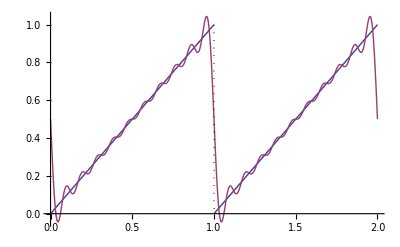

```mathematica
FourierSeries[SawtoothWave[x],x,10,FourierParameters->{1,2Pi}]
Plot[{SawtoothWave[x],%},{x,0,2},ExclusionsStyle->Dotted]
```

The discrete Fourier transform is implemented in Mathematica as follows. Fourier[list] finds the discrete Fourier transform of a list of complex numbers. Multidimensional data can be transformed by 
Fourier[{{x_11, x_12, …, x_(1 n)}, 
         {x_21, x_22, …, x_(2 n)}, …, 
         {x_m1, x_m2, …, x_("mn")}}]. 
If we input exact data, the data will be numericalized to machine precision.

This means that for a vector l of length n, Fourier[l] effectively carries out the matrix product F.l, where the (j,k) element of the square matrix F is n^(-1/2)exp(2π i(k-1)(j-1)/n).

```mathematica
Fourier[{1,1,2,2,1,1,0,0}]
```

{2.82843+0. ⅈ,-0.5+1.20711 ⅈ,0.+0. ⅈ,0.5-0.207107 ⅈ,0.+0. ⅈ,0.5+0.207107 ⅈ,0.+0. ⅈ,-0.5-1.20711 ⅈ}

Here is the Fourier spectrum of the function cos((500+10∑_(k=5)^15 cos(10 k t)/k)t) sampled at the 32769 data points t_k=k 2π/32768

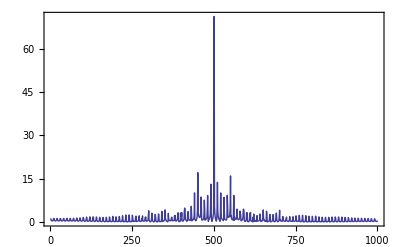

```mathematica
ListPlot[Abs[Take[Fourier[
Table[Evaluate[Cos[(500. +  10 Sum[Cos[k t]/k, {k, 50., 150., 10}]) t]], 
        {t, 0., 2.Pi, 2.Pi/32768}]], 1000]], PlotRange -> All, 
        Joined -> True, Frame -> True, Axes -> False]
```

Application: Frequency Identification
Here is some periodic data with some noise:

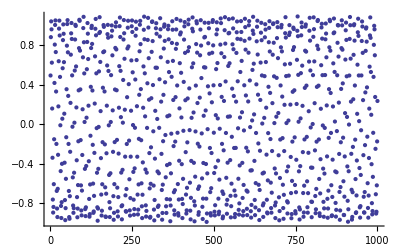

```mathematica
n = 1000;
per = 12.34;
pdata = Table[Sin[2 π x/per], {x,n}] + RandomReal[.1,{n}];
ListPlot[pdata]
```

Find the maximum mode in the spectrum:

```mathematica
f = Abs[Fourier[pdata]];
pos = Position[f, Max[f]][[1,1]]
```

82

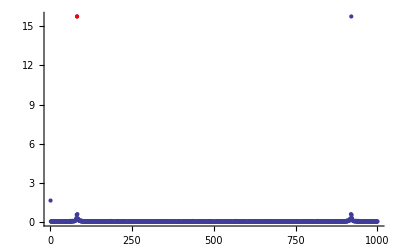

```mathematica
Show[ListPlot[f], Graphics[{Red, Point[{pos, f[[pos]]}]}], PlotRange->All]
```

Two closely related functions to Fourier and InverseFourier are ListConvolve and ListCorrelate

ListConvolve[ker,list]forms the convolution of the kernel ker with list. For a 1D list data of the form {x_1, x_2, …, x_n} and a kernel of the form {y_1, y_2, …, y_m}, the elements z_k of the convolution {z_1, z_2, …, z_(n-m+1)} are z_k=∑_(j=1)^m y_j x_(k-j). Here is a simple symbolic example.

```mathematica
ListConvolve[Table[k[i], {i, 3}], Table[a[i], {i, 8}]]
```

{a[3] k[1]+a[2] k[2]+a[1] k[3],a[4] k[1]+a[3] k[2]+a[2] k[3],a[5] k[1]+a[4] k[2]+a[3] k[3],a[6] k[1]+a[5] k[2]+a[4] k[3],a[7] k[1]+a[6] k[2]+a[5] k[3],a[8] k[1]+a[7] k[2]+a[6] k[3]}

ListCorrelate[ker,list] forms the correlation of the kernel ker with list. With kernel K_r and list a_s, ListCorrelate[ker,list] computes ∑_r K_r a_(s+r), where the limits of the sum are such that the kernel never overhangs either end of the list.

Correlate a kernel {x,y} with a list of data:

```mathematica
ListCorrelate[{x,y},{a,b,c,d,e,f}]
```

{a x+b y,b x+c y,c x+d y,d x+e y,{e x+1.63778 y,e x+0.0396502 y,e x+0.0217963 y,e x+0.037301 y,e x+0.0120282 y,e x+0.0196693 y,e x+0.0226569 y,e x+0.0241759 y,e x+0.0254821 y,e x+0.0639099 y,e x+0.0374473 y,e x+0.0176814 y,e x+0.0242509 y,e x+0.0122191 y,e x+0.0252513 y,e x+0.0357473 y,e x+0.0063855 y,e x+0.0278099 y,e x+0.0021107 y,e x+0.0160667 y,e x+0.0268158 y,e x+0.0390788 y,e x+0.0339053 y,e x+0.0162813 y,e x+0.0401085 y,e x+0.00225214 y,e x+0.0136012 y,e x+0.00820526 y,e x+0.0238481 y,e x+0.0340859 y,e x+0.0258513 y,e x+0.00453714 y,e x+0.0398841 y,e x+0.0566844 y,e x+0.0162063 y,e x+0.0219198 y,e x+0.011767 y,e x+0.0481634 y,e x+0.00835086 y,e x+0.0312304 y,e x+0.0137715 y,e x+0.0204733 y,e x+0.0196978 y,e x+0.0397067 y,e x+0.026965 y,e x+0.0194313 y,e x+0.0525398 y,e x+0.0127126 y,e x+0.0246096 y,e x+0.0324523 y,e x+0.0285172 y,e x+0.00715354 y,e x+0.0137142 y,e x+0.0187971 y,e x+0.0200075 y,e x+0.0158008 y,e x+0.0164728 y,e x+0.0267087 y,e x+0.0538393 y,e x+0.0302162 y,e x+0.0777468 y,e x+0.0375609 y,e x+0.0349349 y,e x+0.0142183 y,e x+0.0293774 y,e x+0.0505054 y,e x+0.0421085 y,e x+0.0854604 y,e x+0.0603224 y,e x+0.0489515 y,e x+0.0413919 y,e x+0.0610119 y,e x+0.0638137 y,e x+0.0499387 y,e x+0.0873704 y,e x+0.0760875 y,e x+0.10436 y,e x+0.121343 y,e x+0.185238 y,e x+0.296133 y,e x+0.546608 y,e x+15.7609 y,e x+0.59472 y,e x+0.281236 y,e x+0.234888 y,e x+0.185313 y,e x+0.138214 y,e x+0.108028 y,e x+0.0865669 y,e x+0.0801984 y,e x+0.0734991 y,e x+0.0714348 y,e x+0.116643 y,e x+0.0425067 y,e x+0.0383889 y,e x+0.0898307 y,e x+0.0346938 y,e x+0.0325298 y,e x+0.0597325 y,e x+0.0558386 y,e x+0.0327679 y,e x+0.0125927 y,e x+0.0128626 y,e x+0.0643095 y,e x+0.0486382 y,e x+0.0254643 y,e x+0.0287662 y,e x+0.0237075 y,e x+0.0269549 y,e x+0.0335811 y,e x+0.0244933 y,e x+0.0674932 y,e x+0.0551873 y,e x+0.0134096 y,e x+0.0230655 y,e x+0.00434766 y,e x+0.0648261 y,e x+0.00902282 y,e x+0.0184202 y,e x+0.0389334 y,e x+0.0214484 y,e x+0.0613574 y,e x+0.00720946 y,e x+0.043491 y,e x+0.039359 y,e x+0.0250795 y,e x+0.0402838 y,e x+0.0142375 y,e x+0.0341879 y,e x+0.0473468 y,e x+0.0158928 y,e x+0.0243514 y,e x+0.0394414 y,e x+0.0406406 y,e x+0.0184903 y,e x+0.0304381 y,e x+0.0138146 y,e x+0.0151303 y,e x+0.0237935 y,e x+0.0235002 y,e x+0.00904828 y,e x+0.0314827 y,e x+0.0110204 y,e x+0.0362092 y,e x+0.0238538 y,e x+0.0580634 y,e x+0.0228531 y,e x+0.0166651 y,e x+0.0284901 y,e x+0.0444298 y,e x+0.00901728 y,e x+0.0256961 y,e x+0.0222898 y,e x+0.0497447 y,e x+0.0208203 y,e x+0.0674474 y,e x+0.0256539 y,e x+0.0110871 y,e x+0.0160717 y,e x+0.0472164 y,e x+0.0345789 y,e x+0.0159017 y,e x+0.0401084 y,e x+0.0603356 y,e x+0.0171223 y,e x+0.0181791 y,e x+0.0595712 y,e x+0.0191921 y,e x+0.0253513 y,e x+0.012853 y,e x+0.0142548 y,e x+0.0297691 y,e x+0.0255582 y,e x+0.0339186 y,e x+0.0224968 y,e x+0.0188219 y,e x+0.0421159 y,e x+0.0674393 y,e x+0.0175555 y,e x+0.0288275 y,e x+0.0033926 y,e x+0.0387796 y,e x+0.0253492 y,e x+0.00545333 y,e x+0.0193232 y,e x+0.0729812 y,e x+0.0337002 y,e x+0.0291265 y,e x+0.0149165 y,e x+0.028568 y,e x+0.0204116 y,e x+0.0374042 y,e x+0.0133199 y,e x+0.0149416 y,e x+0.00373691 y,e x+0.0267771 y,e x+0.00946351 y,e x+0.0174561 y,e x+0.00884074 y,e x+0.0163966 y,e x+0.031015 y,e x+0.0472005 y,e x+0.0595872 y,e x+0.0247499 y,e x+0.0230926 y,e x+0.0689245 y,e x+0.0259789 y,e x+0.0521117 y,e x+0.0475178 y,e x+0.0205485 y,e x+0.0223366 y,e x+0.0201839 y,e x+0.033364 y,e x+0.0316883 y,e x+0.0179706 y,e x+0.0272068 y,e x+0.0221339 y,e x+0.045355 y,e x+0.0346421 y,e x+0.0192027 y,e x+0.0239637 y,e x+0.0126391 y,e x+0.0469301 y,e x+0.0256943 y,e x+0.0141595 y,e x+0.0396132 y,e x+0.063588 y,e x+0.015309 y,e x+0.0648496 y,e x+0.0201591 y,e x+0.0310136 y,e x+0.0233291 y,e x+0.0206616 y,e x+0.0278107 y,e x+0.010945 y,e x+0.00636968 y,e x+0.018567 y,e x+0.00838079 y,e x+0.0276174 y,e x+0.0332171 y,e x+0.0140645 y,e x+0.0314124 y,e x+0.0342591 y,e x+0.00904968 y,e x+0.0174962 y,e x+0.0462041 y,e x+0.0239127 y,e x+0.0383771 y,e x+0.0225343 y,e x+0.00544949 y,e x+0.0311342 y,e x+0.0318881 y,e x+0.0262528 y,e x+0.0356063 y,e x+0.0233908 y,e x+0.0110219 y,e x+0.0175085 y,e x+0.0238739 y,e x+0.0142484 y,e x+0.0486638 y,e x+0.00574688 y,e x+0.0552134 y,e x+0.04216 y,e x+0.0102291 y,e x+0.0185724 y,e x+0.0111572 y,e x+0.00866422 y,e x+0.0408869 y,e x+0.0398148 y,e x+0.0119886 y,e x+0.0191424 y,e x+0.00725379 y,e x+0.0154093 y,e x+0.0073212 y,e x+0.0238733 y,e x+0.0233476 y,e x+0.0624194 y,e x+0.0285262 y,e x+0.0422834 y,e x+0.0392095 y,e x+0.0175444 y,e x+0.0252392 y,e x+0.0190818 y,e x+0.023444 y,e x+0.00363354 y,e x+0.0378411 y,e x+0.0272621 y,e x+0.00750761 y,e x+0.0183607 y,e x+0.0272945 y,e x+0.0281522 y,e x+0.0157372 y,e x+0.0254882 y,e x+0.0363444 y,e x+0.028216 y,e x+0.0205287 y,e x+0.0191647 y,e x+0.0195358 y,e x+0.0229782 y,e x+0.0295823 y,e x+0.0344756 y,e x+0.0213069 y,e x+0.0212604 y,e x+0.0295254 y,e x+0.0123161 y,e x+0.0539739 y,e x+0.0261317 y,e x+0.0321104 y,e x+0.0225299 y,e x+0.0240851 y,e x+0.0267582 y,e x+0.0247128 y,e x+0.0170221 y,e x+0.0170862 y,e x+0.0217229 y,e x+0.0297546 y,e x+0.024352 y,e x+0.0173131 y,e x+0.0263925 y,e x+0.0135693 y,e x+0.028805 y,e x+0.0328517 y,e x+0.0251725 y,e x+0.0303222 y,e x+0.024323 y,e x+0.0380465 y,e x+0.0278092 y,e x+0.0286963 y,e x+0.0226478 y,e x+0.0128538 y,e x+0.026688 y,e x+0.0311111 y,e x+0.00853099 y,e x+0.0566887 y,e x+0.0305694 y,e x+0.0235828 y,e x+0.0236468 y,e x+0.0166419 y,e x+0.0262217 y,e x+0.011725 y,e x+0.0491472 y,e x+0.0392282 y,e x+0.00516849 y,e x+0.0177248 y,e x+0.0460494 y,e x+0.0366602 y,e x+0.0273757 y,e x+0.054156 y,e x+0.0277055 y,e x+0.0296046 y,e x+0.0270331 y,e x+0.0287644 y,e x+0.0329931 y,e x+0.0162104 y,e x+0.049909 y,e x+0.0321027 y,e x+0.00909651 y,e x+0.0291135 y,e x+0.0206268 y,e x+0.0262232 y,e x+0.033512 y,e x+0.0352871 y,e x+0.00416247 y,e x+0.0387356 y,e x+0.019138 y,e x+0.0053669 y,e x+0.0170271 y,e x+0.024335 y,e x+0.0240492 y,e x+0.0430702 y,e x+0.00623435 y,e x+0.0348333 y,e x+0.0234573 y,e x+0.01149 y,e x+0.0475613 y,e x+0.033532 y,e x+0.021785 y,e x+0.0288886 y,e x+0.0333729 y,e x+0.0397502 y,e x+0.00488322 y,e x+0.0196054 y,e x+0.0058028 y,e x+0.0167999 y,e x+0.0250059 y,e x+0.0217747 y,e x+0.00804297 y,e x+0.028757 y,e x+0.0438975 y,e x+0.0288909 y,e x+0.0206561 y,e x+0.0137107 y,e x+0.0122249 y,e x+0.0385201 y,e x+0.0457893 y,e x+0.0231995 y,e x+0.00938879 y,e x+0.0181142 y,e x+0.0225169 y,e x+0.00952949 y,e x+0.0108792 y,e x+0.0128235 y,e x+0.0286756 y,e x+0.01602 y,e x+0.0286717 y,e x+0.0177893 y,e x+0.00138048 y,e x+0.00641406 y,e x+0.0634909 y,e x+0.00689618 y,e x+0.0312883 y,e x+0.0377841 y,e x+0.0168395 y,e x+0.0209596 y,e x+0.0224003 y,e x+0.0248763 y,e x+0.0172843 y,e x+0.0305178 y,e x+0.0111292 y,e x+0.0239033 y,e x+0.0144014 y,e x+0.0442663 y,e x+0.0190786 y,e x+0.0312281 y,e x+0.0171984 y,e x+0.0487181 y,e x+0.0528144 y,e x+0.0282074 y,e x+0.0208626 y,e x+0.0251471 y,e x+0.0363115 y,e x+0.0221586 y,e x+0.0374707 y,e x+0.026912 y,e x+0.0708209 y,e x+0.0486734 y,e x+0.0156538 y,e x+0.0382169 y,e x+0.06152 y,e x+0.0273241 y,e x+0.00477816 y,e x+0.0158091 y,e x+0.00864328 y,e x+0.0217228 y,e x+0.0130569 y,e x+0.0237757 y,e x+0.00502054 y,e x+0.00851243 y,e x+0.0185026 y,e x+0.0124799 y,e x+0.0484299 y,e x+0.0258462 y,e x+0.0348375 y,e x+0.0127829 y,e x+0.0342888 y,e x+0.0419253 y,e x+0.0322277 y,e x+0.0265574 y,e x+0.00490619 y,e x+0.0089678 y,e x+0.042712 y,e x+0.0187272 y,e x+0.0240032 y,e x+0.0421085 y,e x+0.0232966 y,e x+0.053578 y,e x+0.000691267 y,e x+0.0211475 y,e x+0.0456606 y,e x+0.0195148 y,e x+0.00952499 y,e x+0.0163578 y,e x+0.0264395 y,e x+0.00568195 y,e x+0.0312024 y,e x+0.00256477 y,e x+0.021085 y,e x+0.0329371 y,e x+0.0193006 y,e x+0.0310163 y,e x+0.0258698 y,e x+0.0133697 y,e x+0.0396711 y,e x+0.0288892 y,e x+0.0242829 y,e x+0.0196032 y,e x+0.0266912 y,e x+0.0170981 y,e x+0.0103619 y,e x+0.0606753 y,e x+0.0170642 y,e x+0.0279225 y,e x+0.0346104 y,e x+0.0246592 y,e x+0.0216235 y,e x+0.0430324 y,e x+0.0117128 y,e x+0.00845772 y,e x+0.0224666 y,e x+0.00471868 y,e x+0.0138443 y,e x+0.00471868 y,e x+0.0224666 y,e x+0.00845772 y,e x+0.0117128 y,e x+0.0430324 y,e x+0.0216235 y,e x+0.0246592 y,e x+0.0346104 y,e x+0.0279225 y,e x+0.0170642 y,e x+0.0606753 y,e x+0.0103619 y,e x+0.0170981 y,e x+0.0266912 y,e x+0.0196032 y,e x+0.0242829 y,e x+0.0288892 y,e x+0.0396711 y,e x+0.0133697 y,e x+0.0258698 y,e x+0.0310163 y,e x+0.0193006 y,e x+0.0329371 y,e x+0.021085 y,e x+0.00256477 y,e x+0.0312024 y,e x+0.00568195 y,e x+0.0264395 y,e x+0.0163578 y,e x+0.00952499 y,e x+0.0195148 y,e x+0.0456606 y,e x+0.0211475 y,e x+0.000691267 y,e x+0.053578 y,e x+0.0232966 y,e x+0.0421085 y,e x+0.0240032 y,e x+0.0187272 y,e x+0.042712 y,e x+0.0089678 y,e x+0.00490619 y,e x+0.0265574 y,e x+0.0322277 y,e x+0.0419253 y,e x+0.0342888 y,e x+0.0127829 y,e x+0.0348375 y,e x+0.0258462 y,e x+0.0484299 y,e x+0.0124799 y,e x+0.0185026 y,e x+0.00851243 y,e x+0.00502054 y,e x+0.0237757 y,e x+0.0130569 y,e x+0.0217228 y,e x+0.00864328 y,e x+0.0158091 y,e x+0.00477816 y,e x+0.0273241 y,e x+0.06152 y,e x+0.0382169 y,e x+0.0156538 y,e x+0.0486734 y,e x+0.0708209 y,e x+0.026912 y,e x+0.0374707 y,e x+0.0221586 y,e x+0.0363115 y,e x+0.0251471 y,e x+0.0208626 y,e x+0.0282074 y,e x+0.0528144 y,e x+0.0487181 y,e x+0.0171984 y,e x+0.0312281 y,e x+0.0190786 y,e x+0.0442663 y,e x+0.0144014 y,e x+0.0239033 y,e x+0.0111292 y,e x+0.0305178 y,e x+0.0172843 y,e x+0.0248763 y,e x+0.0224003 y,e x+0.0209596 y,e x+0.0168395 y,e x+0.0377841 y,e x+0.0312883 y,e x+0.00689618 y,e x+0.0634909 y,e x+0.00641406 y,e x+0.00138048 y,e x+0.0177893 y,e x+0.0286717 y,e x+0.01602 y,e x+0.0286756 y,e x+0.0128235 y,e x+0.0108792 y,e x+0.00952949 y,e x+0.0225169 y,e x+0.0181142 y,e x+0.00938879 y,e x+0.0231995 y,e x+0.0457893 y,e x+0.0385201 y,e x+0.0122249 y,e x+0.0137107 y,e x+0.0206561 y,e x+0.0288909 y,e x+0.0438975 y,e x+0.028757 y,e x+0.00804297 y,e x+0.0217747 y,e x+0.0250059 y,e x+0.0167999 y,e x+0.0058028 y,e x+0.0196054 y,e x+0.00488322 y,e x+0.0397502 y,e x+0.0333729 y,e x+0.0288886 y,e x+0.021785 y,e x+0.033532 y,e x+0.0475613 y,e x+0.01149 y,e x+0.0234573 y,e x+0.0348333 y,e x+0.00623435 y,e x+0.0430702 y,e x+0.0240492 y,e x+0.024335 y,e x+0.0170271 y,e x+0.0053669 y,e x+0.019138 y,e x+0.0387356 y,e x+0.00416247 y,e x+0.0352871 y,e x+0.033512 y,e x+0.0262232 y,e x+0.0206268 y,e x+0.0291135 y,e x+0.00909651 y,e x+0.0321027 y,e x+0.049909 y,e x+0.0162104 y,e x+0.0329931 y,e x+0.0287644 y,e x+0.0270331 y,e x+0.0296046 y,e x+0.0277055 y,e x+0.054156 y,e x+0.0273757 y,e x+0.0366602 y,e x+0.0460494 y,e x+0.0177248 y,e x+0.00516849 y,e x+0.0392282 y,e x+0.0491472 y,e x+0.011725 y,e x+0.0262217 y,e x+0.0166419 y,e x+0.0236468 y,e x+0.0235828 y,e x+0.0305694 y,e x+0.0566887 y,e x+0.00853099 y,e x+0.0311111 y,e x+0.026688 y,e x+0.0128538 y,e x+0.0226478 y,e x+0.0286963 y,e x+0.0278092 y,e x+0.0380465 y,e x+0.024323 y,e x+0.0303222 y,e x+0.0251725 y,e x+0.0328517 y,e x+0.028805 y,e x+0.0135693 y,e x+0.0263925 y,e x+0.0173131 y,e x+0.024352 y,e x+0.0297546 y,e x+0.0217229 y,e x+0.0170862 y,e x+0.0170221 y,e x+0.0247128 y,e x+0.0267582 y,e x+0.0240851 y,e x+0.0225299 y,e x+0.0321104 y,e x+0.0261317 y,e x+0.0539739 y,e x+0.0123161 y,e x+0.0295254 y,e x+0.0212604 y,e x+0.0213069 y,e x+0.0344756 y,e x+0.0295823 y,e x+0.0229782 y,e x+0.0195358 y,e x+0.0191647 y,e x+0.0205287 y,e x+0.028216 y,e x+0.0363444 y,e x+0.0254882 y,e x+0.0157372 y,e x+0.0281522 y,e x+0.0272945 y,e x+0.0183607 y,e x+0.00750761 y,e x+0.0272621 y,e x+0.0378411 y,e x+0.00363354 y,e x+0.023444 y,e x+0.0190818 y,e x+0.0252392 y,e x+0.0175444 y,e x+0.0392095 y,e x+0.0422834 y,e x+0.0285262 y,e x+0.0624194 y,e x+0.0233476 y,e x+0.0238733 y,e x+0.0073212 y,e x+0.0154093 y,e x+0.00725379 y,e x+0.0191424 y,e x+0.0119886 y,e x+0.0398148 y,e x+0.0408869 y,e x+0.00866422 y,e x+0.0111572 y,e x+0.0185724 y,e x+0.0102291 y,e x+0.04216 y,e x+0.0552134 y,e x+0.00574688 y,e x+0.0486638 y,e x+0.0142484 y,e x+0.0238739 y,e x+0.0175085 y,e x+0.0110219 y,e x+0.0233908 y,e x+0.0356063 y,e x+0.0262528 y,e x+0.0318881 y,e x+0.0311342 y,e x+0.00544949 y,e x+0.0225343 y,e x+0.0383771 y,e x+0.0239127 y,e x+0.0462041 y,e x+0.0174962 y,e x+0.00904968 y,e x+0.0342591 y,e x+0.0314124 y,e x+0.0140645 y,e x+0.0332171 y,e x+0.0276174 y,e x+0.00838079 y,e x+0.018567 y,e x+0.00636968 y,e x+0.010945 y,e x+0.0278107 y,e x+0.0206616 y,e x+0.0233291 y,e x+0.0310136 y,e x+0.0201591 y,e x+0.0648496 y,e x+0.015309 y,e x+0.063588 y,e x+0.0396132 y,e x+0.0141595 y,e x+0.0256943 y,e x+0.0469301 y,e x+0.0126391 y,e x+0.0239637 y,e x+0.0192027 y,e x+0.0346421 y,e x+0.045355 y,e x+0.0221339 y,e x+0.0272068 y,e x+0.0179706 y,e x+0.0316883 y,e x+0.033364 y,e x+0.0201839 y,e x+0.0223366 y,e x+0.0205485 y,e x+0.0475178 y,e x+0.0521117 y,e x+0.0259789 y,e x+0.0689245 y,e x+0.0230926 y,e x+0.0247499 y,e x+0.0595872 y,e x+0.0472005 y,e x+0.031015 y,e x+0.0163966 y,e x+0.00884074 y,e x+0.0174561 y,e x+0.00946351 y,e x+0.0267771 y,e x+0.00373691 y,e x+0.0149416 y,e x+0.0133199 y,e x+0.0374042 y,e x+0.0204116 y,e x+0.028568 y,e x+0.0149165 y,e x+0.0291265 y,e x+0.0337002 y,e x+0.0729812 y,e x+0.0193232 y,e x+0.00545333 y,e x+0.0253492 y,e x+0.0387796 y,e x+0.0033926 y,e x+0.0288275 y,e x+0.0175555 y,e x+0.0674393 y,e x+0.0421159 y,e x+0.0188219 y,e x+0.0224968 y,e x+0.0339186 y,e x+0.0255582 y,e x+0.0297691 y,e x+0.0142548 y,e x+0.012853 y,e x+0.0253513 y,e x+0.0191921 y,e x+0.0595712 y,e x+0.0181791 y,e x+0.0171223 y,e x+0.0603356 y,e x+0.0401084 y,e x+0.0159017 y,e x+0.0345789 y,e x+0.0472164 y,e x+0.0160717 y,e x+0.0110871 y,e x+0.0256539 y,e x+0.0674474 y,e x+0.0208203 y,e x+0.0497447 y,e x+0.0222898 y,e x+0.0256961 y,e x+0.00901728 y,e x+0.0444298 y,e x+0.0284901 y,e x+0.0166651 y,e x+0.0228531 y,e x+0.0580634 y,e x+0.0238538 y,e x+0.0362092 y,e x+0.0110204 y,e x+0.0314827 y,e x+0.00904828 y,e x+0.0235002 y,e x+0.0237935 y,e x+0.0151303 y,e x+0.0138146 y,e x+0.0304381 y,e x+0.0184903 y,e x+0.0406406 y,e x+0.0394414 y,e x+0.0243514 y,e x+0.0158928 y,e x+0.0473468 y,e x+0.0341879 y,e x+0.0142375 y,e x+0.0402838 y,e x+0.0250795 y,e x+0.039359 y,e x+0.043491 y,e x+0.00720946 y,e x+0.0613574 y,e x+0.0214484 y,e x+0.0389334 y,e x+0.0184202 y,e x+0.00902282 y,e x+0.0648261 y,e x+0.00434766 y,e x+0.0230655 y,e x+0.0134096 y,e x+0.0551873 y,e x+0.0674932 y,e x+0.0244933 y,e x+0.0335811 y,e x+0.0269549 y,e x+0.0237075 y,e x+0.0287662 y,e x+0.0254643 y,e x+0.0486382 y,e x+0.0643095 y,e x+0.0128626 y,e x+0.0125927 y,e x+0.0327679 y,e x+0.0558386 y,e x+0.0597325 y,e x+0.0325298 y,e x+0.0346938 y,e x+0.0898307 y,e x+0.0383889 y,e x+0.0425067 y,e x+0.116643 y,e x+0.0714348 y,e x+0.0734991 y,e x+0.0801984 y,e x+0.0865669 y,e x+0.108028 y,e x+0.138214 y,e x+0.185313 y,e x+0.234888 y,e x+0.281236 y,e x+0.59472 y,e x+15.7609 y,e x+0.546608 y,e x+0.296133 y,e x+0.185238 y,e x+0.121343 y,e x+0.10436 y,e x+0.0760875 y,e x+0.0873704 y,e x+0.0499387 y,e x+0.0638137 y,e x+0.0610119 y,e x+0.0413919 y,e x+0.0489515 y,e x+0.0603224 y,e x+0.0854604 y,e x+0.0421085 y,e x+0.0505054 y,e x+0.0293774 y,e x+0.0142183 y,e x+0.0349349 y,e x+0.0375609 y,e x+0.0777468 y,e x+0.0302162 y,e x+0.0538393 y,e x+0.0267087 y,e x+0.0164728 y,e x+0.0158008 y,e x+0.0200075 y,e x+0.0187971 y,e x+0.0137142 y,e x+0.00715354 y,e x+0.0285172 y,e x+0.0324523 y,e x+0.0246096 y,e x+0.0127126 y,e x+0.0525398 y,e x+0.0194313 y,e x+0.026965 y,e x+0.0397067 y,e x+0.0196978 y,e x+0.0204733 y,e x+0.0137715 y,e x+0.0312304 y,e x+0.00835086 y,e x+0.0481634 y,e x+0.011767 y,e x+0.0219198 y,e x+0.0162063 y,e x+0.0566844 y,e x+0.0398841 y,e x+0.00453714 y,e x+0.0258513 y,e x+0.0340859 y,e x+0.0238481 y,e x+0.00820526 y,e x+0.0136012 y,e x+0.00225214 y,e x+0.0401085 y,e x+0.0162813 y,e x+0.0339053 y,e x+0.0390788 y,e x+0.0268158 y,e x+0.0160667 y,e x+0.0021107 y,e x+0.0278099 y,e x+0.0063855 y,e x+0.0357473 y,e x+0.0252513 y,e x+0.0122191 y,e x+0.0242509 y,e x+0.0176814 y,e x+0.0374473 y,e x+0.0639099 y,e x+0.0254821 y,e x+0.0241759 y,e x+0.0226569 y,e x+0.0196693 y,e x+0.0120282 y,e x+0.037301 y,e x+0.0217963 y,e x+0.0396502 y}}

Two-dimensional correlation:

```mathematica
ListCorrelate[{{1,1},{1,1}},{{a,b,c},{d,e,f},{g,h,i}}]
```

{{a+b+d+e,{1.63778+b+c+e,0.0396502+b+c+e,0.0217963+b+c+e,0.037301+b+c+e,«993»,0.037301+b+c+e,0.0217963+b+c+e,0.0396502+b+c+e}},{d+e+g+h,{«1»}}}

Application: Smooth data with a weighted running average:

```mathematica
x = N[Range[1000]/1000];
data = RandomReal[{-1,1}, 1000] +2  Sin[7 x];
```

Normalized Gaussian profile for averaging weights:

```mathematica
w = Exp[-.01 N[Range[-24,24]^2]];
w /= Total[w];
```

```mathematica
smoother = ListCorrelate[w, data];
```

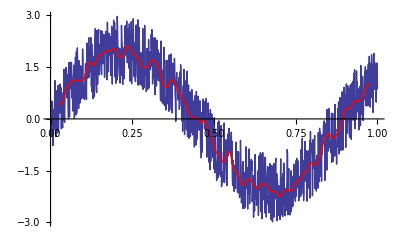

```mathematica
Show[ListLinePlot[Transpose[{x,data}]], ListLinePlot[Transpose[{Take[x,{25,-25}],smoother}], PlotStyle->Red]]
```

```mathematica
Clear[x,w,smoother];
```

Gaussian smoothing of an image:

```mathematica
SetDirectory[NotebookDirectory[]];
img = ReadList["ExampleData/fish.data",Number,RecordLists->True];
```

Gaussian kernel with a 5×5 pixel stencil:

```mathematica
g[σ_][x_, y_] := 1/(2 π σ^2)Exp[-1/(2 σ^2)(x^2 + y^2)];
gk = N[Outer[g[1], Range[-2,2], Range[-2,2]]];
```

Smooth the image:

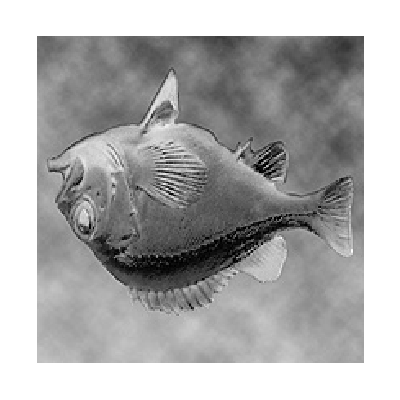
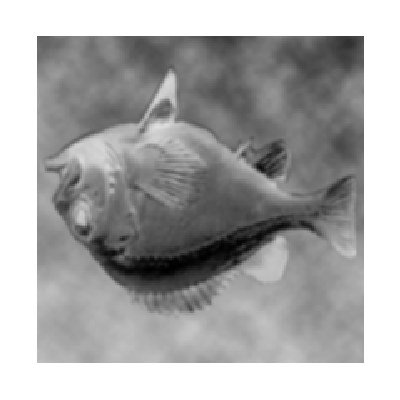

```mathematica
smooth = ListCorrelate[gk, img];
{ArrayPlot@img,ArrayPlot@smooth}
```

Edge detection in an image: Correlate with a Laplacian filter kernel:

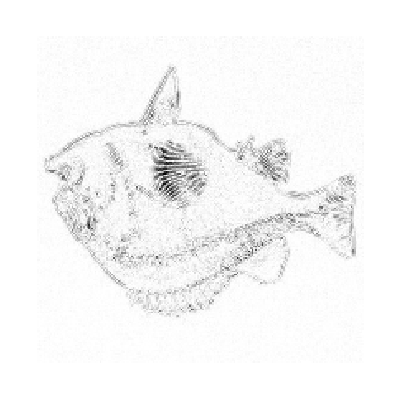
{-Graphics-,-Graphics-}

```mathematica
edge=ListCorrelate[{{1,0,1},{0,-4,0},{1,0,1}},img];
{ArrayPlot@img,ArrayPlot@edge}
```

### Excercise

Find the total length of the Lissajous knot parametrized by
x(t)=cos(2t)
y(t)=cos(3t + π/4)
z(t)=cos(5t + 2)
(Hint: calculate the norm of the velocity vector and integrate it to get the length.)

Find the mass of a thin disk of radius 1 whose density r units from the center is given by δ=√(1/4+r^2).

Find the area of one “leaf” of the curve given in polar coordinates as r(θ)=sin(3θ) (Remember that in polar coordinates the element of area is given by dA = r dr dθ.)

Find the limits of (sin x^2)/xas x→0.

Find the closest point on the hyperbola x^2 − y^2 == 1 to the point (3, 5).

Compare symbolic and numerical evaluations of ∫_0^1 (ω^4 ⅇ^ω)/((ⅇ^ω-1)^2).

Evaluate ∫_0^∞ (ω^4 ⅇ^ω)/((ⅇ^ω-1)^2) numerically.  [Hint: use LogPlot to examine the integrand.]

Interference maxima
If n equally spaced identical antennas radiate in phase, the angular distribution is described by an interference pattern of the form
f[n,α]=Sin[n α]^2/Sin[α]^2
where
α = d/λ Sin[θ]
and where d is the spacing between sources and λ is the wave length.
a) Plot the distribution in α for several values of n and determine the locations of the principal maxima.  How many minor maxima are found between principal maxima?
b) Write a function which produces a numerical list of positions for the minor maxima. with 0<α<π.